d.) Display the output of the rules acting on the x,y coordinates written in base 2, say on an array of size 64 by 64.  Try for instance the 36118th rule (with no convention, it is possible a different numbering scheme will behave differently).

```mathematica
regola={{0,{0,0}}->{0},{0,{0,1}}->{0},{0,{1,0}}->{1},{0,{1,1}}->{2},{1,{0,0}}->{1},{1,{0,1}}->{1},{1,{1,0}}->{1},{1,{1,1}}->{1},{2,{0,0}}->{2},{2,{0,1}}->{2},{2,{1,0}}->{0},{2,{1,1}}->{1}}
```

{{0,{0,0}}→{0},{0,{0,1}}→{0},{0,{1,0}}→{1},{0,{1,1}}→{2},{1,{0,0}}→{1},{1,{0,1}}→{1},{1,{1,0}}→{1},{1,{1,1}}→{1},{2,{0,0}}→{2},{2,{0,1}}→{2},{2,{1,0}}→{0},{2,{1,1}}→{1}}

```mathematica
crea[stato_]:= {stato,#}& /@ {{0,0},{0,1},{1,0},{1,1}}
```

```mathematica
trasforma[stato_]:= Flatten[crea[stato]/. regola]
```

```mathematica
inizio= {{0}}
```

{{0}}

```mathematica
trasforma[0]
```

{0,0,1,2}

```mathematica
crea[#]& /@ {0,0,1,2}
```

{{{0,{0,0}},{0,{0,1}},{0,{1,0}},{0,{1,1}}},{{0,{0,0}},{0,{0,1}},{0,{1,0}},{0,{1,1}}},{{1,{0,0}},{1,{0,1}},{1,{1,0}},{1,{1,1}}},{{2,{0,0}},{2,{0,1}},{2,{1,0}},{2,{1,1}}}}

```mathematica
trasforma2[0]
```

trasforma2[0]

```mathematica
trasforma2[stati_]:= Flatten[trasforma[#]& /@ stati]
```

```mathematica
trasforma2[trasforma[#]& /@ {0,0,1,2}]
```

{0,0,1,2,0,0,0,0,1,2,0,1,0,0,1,2,1,0,0,0,1,2,1,1,0,0,1,2,0,0,0,0,1,2,0,1,0,0,1,2,1,0,0,0,1,2,1,1,1,1,1,1,0,0,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,2,2,0,1,0,0,2,2,0,1,0,1,2,2,0,1,1,0,2,2,0,1,1,1}

```mathematica
trasforma[#]& /@ {0,0,1,2}
```

{{0,0,1,2},{0,0,1,2},{1,1,1,1},{2,2,0,1}}

```mathematica
NestList[trasforma2 ,{0},2]
```

{{0},{0,0,1,2},{0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1}}

```mathematica
stati=Nest[trasforma2,{0},6]
```

{0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[stati]
```

4096

```mathematica
64*64
```

4096

```mathematica
(* each state is quadruplicate at each step, so we have 4^steps final states *)
```

```mathematica
4^6
```

4096

```mathematica
m=Module[{L=Sqrt[Length[stati]]},Table[no,{i,L},{j,L}]]//MatrixForm
```

(no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no
no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no | no)

```mathematica
ex1= Nest[trasforma2,{0},2]
```

{0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1}

```mathematica
Length[ex1]
```

16

```mathematica
ex2=Nest[trasforma2,{0},3]
```

{0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,0,1,2,2,0,1,0,0,1,2,1,1,1,1}

```mathematica
Length[ex2]
```

```mathematica
(*quanti quadrati 2x2?*)
```

```mathematica
64/4
```

16

```mathematica
(*Quante rghe/colonne?*)
```

```mathematica
Sqrt[16]
```

4

```mathematica
Module[{L=Length[ex1],colonna=1,riga=1,st=ex1},(m=Table[no,{i,Sqrt[L]},{j,Sqrt[L]}];Table[(If[Mod[i,4]==0,m[[riga+1,colonna+1]]= st[[i]],If[Mod[i,4]==2,m[[riga,colonna+1]]=st[[i]],If[Mod[i,4]==3,m[[riga+1,colonna]]=st[[i]],m[[riga,colonna]]=st[[i]]]]];If[(Mod[i,4]==0&& Mod[i,2Sqrt[L]]≠0),(colonna=colonna+2;Print[colonna]),If[(Mod[i,4]==0&&Mod[i,2Sqrt[L]]==0),(riga=riga+2;colonna=colonna-2;Print[riga]),Null]]),{i,L}])]
```

3

3

3

5

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
m
```

{{0,0,0,0},{1,2,1,2},{1,1,2,2},{1,1,0,1}}

```mathematica
.10
```

```mathematica
{{0,0,0,0},{1,2,1,2},{no,no,1,1},{no,no,1,1}}//MatrixForm
```

(0 | 0 | 0 | 0
1 | 2 | 1 | 2
no | no | 1 | 1
no | no | 1 | 1)

```mathematica
Mod[2,4]
```

2

```mathematica
Mod
```

Mod

```mathematica
Mod[5,4]
```

1

```mathematica
Mod[9,4]
```

1

```mathematica
Sqrt[16]
```

4

```mathematica
createquad[states_]:=Module[{L=Length[states],colonna=1,riga=1,st=states},(m=Table[no,{i,Sqrt[L]},{j,Sqrt[L]}];Table[(If[Mod[i,4]==0,m[[riga+1,colonna+1]]= st[[i]],If[Mod[i,4]==2,m[[riga,colonna+1]]=st[[i]],If[Mod[i,4]==3,m[[riga+1,colonna]]=st[[i]],m[[riga,colonna]]=st[[i]]]]];If[(Mod[i,4]==0&& Mod[i,2Sqrt[L]]≠0),(colonna=colonna+2;),If[(Mod[i,4]==0&&Mod[i,2Sqrt[L]]==0),(riga=riga+2;colonna=colonna-2;),(colonna=colonna;riga=riga;)]]),{i,L}])]
```

```mathematica
s=Nest[trasforma2,{0},6];
```

```mathematica
createquad[s]
```

```mathematica
Module[{L=Length[ex1],colonna=1,riga=1,st=ex1},(m=Table[no,{i,Sqrt[L]},{j,Sqrt[L]}];Table[(If[Mod[i,4]==0,m[[riga+1,colonna+1]]= st[[i]],If[Mod[i,4]==2,m[[riga,colonna+1]]=st[[i]],If[Mod[i,4]==3,m[[riga+1,colonna]]=st[[i]],m[[riga,colonna]]=st[[i]]]]];If[(Mod[i,4]==0&& Mod[i,2Sqrt[L]]≠0),(colonna=colonna+2;Print[colonna]),If[(Mod[i,4]==0&&Mod[i,2Sqrt[L]]==0),(riga=riga+2;colonna=colonna-2;Print[riga]),Null]]),{i,L}])]
```

```mathematica
Module[{L=Length[ex1],colonna=1,riga=1,st=ex1},(m=Table[no,{i,Sqrt[L]},{j,Sqrt[L]}];Map[(If[Mod[#1,4]==0,m[[riga+1,colonna+1]]= st[[#]],If[Mod[#,4]==2,m[[riga,colonna+1]]=st[[#]],If[Mod[#,4]==3,m[[riga+1,colonna]]=st[[#]],m[[riga,colonna]]=st[[#]]]]];If[(Mod[#,4]==0&& Mod[#,2Sqrt[L]]≠0),(colonna=colonna+2;Print[colonna]),If[(Mod[#,4]==0&&Mod[#,2Sqrt[L]]==0),(riga=riga+2;colonna=colonna-2;Print[riga]),(riga=riga;colonna=colonna;)]])&,Range[1,Length[st]]])]
```

3

3

3

5

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
m
```

{{0,0,0,0},{1,2,1,2},{1,1,2,2},{1,1,0,1}}

```mathematica
(If[Mod[#1,4]==0,m[[riga+1,colonna+1]]= st[[#]],If[Mod[#,4]==2,m[[riga,colonna+1]]=st[[#]],If[Mod[#,4]==3,m[[riga+1,colonna]]=st[[#]],m[[riga,colonna]]=st[[#]]]]];If[(Mod[#,4]==0&& Mod[#,2Sqrt[L]]≠0),(colonna=colonna+2;Print[colonna]),If[(Mod[#,4]==0&&Mod[#,2Sqrt[L]]==0),(riga=riga+2;colonna=colonna-2;Print[riga]),(riga=riga;colonna=colonna;)]])& @@ Range[1,{Length[st]}]
```

```mathematica
Partition[ex1,4]
```

{{0,0,1,2},{0,0,1,2},{1,1,1,1},{2,2,0,1}}

```mathematica
matrice[a_]:= {{a[[1]],a[[2]]},{a[[3]],a[[4]]}}
```

```mathematica
matrice /@ Partition[ex1,4] //MatrixForm
```

((0
0) | (1
2)
(0
0) | (1
2)
(1
1) | (1
1)
(2
2) | (0
1))

```mathematica
?:>
```

lhs:>rhs or lhs:>rhs represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used.

```mathematica
{1,2,3,4} /.{a_,b_,c_,d_}:>{{a,b},{b,c}}
```

{{1,2},{2,3}}

```mathematica
{a,b,c,d}:>{{a,b},{b,c}}
```

{a,b,c,d}:>{{a,b},{b,c}}

```mathematica
(# /. {a_,b_,c_,d_}:>{{a,b},{b,c}})&  /@ Partition[ex1,4]
```

{{{0,0},{0,1}},{{0,0},{0,1}},{{1,1},{1,1}},{{2,2},{2,0}}}

```mathematica
%//Transpose
```

{{{0,0},{0,0},{1,1},{2,2}},{{0,1},{0,1},{1,1},{2,0}}}

```mathematica
%//MatrixForm
```

((0
0) | (0
0) | (1
1) | (2
2)
(0
1) | (0
1) | (1
1) | (2
0))

```mathematica
trasf[m_]:= m/. {a_,b_,c_,d_}:>{{a,b},{b,c}}
```

```mathematica
trasf[{1,2,3,4}]
```

{{1,2},{2,3}}

```mathematica
pp={{1,2},{1,2}}
```

{{1,2},{1,2}}

```mathematica
ReplacePart[pp,{1,2}->{1,2}]
```

```mathematica
e=Nest[trasforma2,{0},2]
```

{0,0,1,2,0,0,1,2,1,1,1,1,2,2,0,1}

```mathematica
e2=Partition[e,2]
```

{{0,0},{1,2},{0,0},{1,2},{1,1},{1,1},{2,2},{0,1}}

```mathematica
OddQ[1]
```

True

```mathematica
Length[e2]
```

8

```mathematica
p={}
```

{}

```mathematica
d={}
```

{}

```mathematica
creamatrice[stati_]:= Module[{p={},d={},s=Partition[stati,2]},Table[If[EvenQ[i],AppendTo[p,s[[i]]],AppendTo[d,s[[i]]]],{i,Length[s]}];With[{L=Sqrt[Length[stati]]},{Partition[Flatten[d],L],Partition[Flatten[p],L]}]]
```

```mathematica
creamatrice[e]
```

{{{0,0,0,0},{1,1,2,2}},{{1,2,1,2},{1,1,0,1}}}

```mathematica
Table[If[EvenQ[i],p=Append[p,e2[[i]]],d=Append[d,e2[[i]]]],{i,Length[e2]}]
```

{{{0,0}},{{1,2}},{{0,0},{0,0}},{{1,2},{1,2}},{{0,0},{0,0},{1,1}},{{1,2},{1,2},{1,1}},{{0,0},{0,0},{1,1},{2,2}},{{1,2},{1,2},{1,1},{0,1}}}

```mathematica
p
```

{{1,2},{1,2},{1,1},{0,1}}

```mathematica
d
```

{{0,0},{0,0},{1,1},{2,2}}

```mathematica
Partition[Flatten[p],4]
```

{{1,2,1,2},{1,1,0,1}}

```mathematica
MapThread[{#,#2}&,{{1,2},{3,4}}]
```

{{1,3},{2,4}}

```mathematica
creamatrice[e]
```

{{{1,2,1,2},{1,1,0,1}},{{0,0,0,0},{1,1,2,2}}}

```mathematica
Riffle[#,#2]& @@ creamatrice[e]
```

{{1,2,1,2},{0,0,0,0},{1,1,0,1},{1,1,2,2}}

```mathematica
creamatrice2[stati_]:= Module[{p={},d={},s=Partition[stati,2]},Table[If[EvenQ[i],p=Append[p,s[[i]]],d=Append[d,s[[i]]]],{i,Length[s]}];With[{L=Sqrt[Length[stati]]},Riffle[Partition[Flatten[d],L],Partition[Flatten[p],L]]]]
```

```mathematica
creamatrice2[e]
```

{{0,0,0,0},{1,2,1,2},{1,1,2,2},{1,1,0,1}}

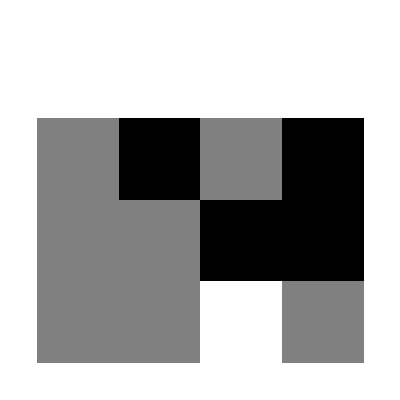

```mathematica
ArrayPlot[creamatrice2[e]]
```

```mathematica
IntegerDigits[17,2,6]
```

{0,1,0,0,0,1}